```mathematica
<<SimulationTools`
```

## Exact gaussian solution

```mathematica
ClearAll[baseGaussian,baseGaussianDX];
baseGaussian[x_,sigma_]:=Exp[-1/2*(x/sigma)^2];
baseGaussianDX[x_,sigma_]:=-x/sigma^2*baseGaussian[x,sigma];

ClearAll[gaussianSolution,gaussianSolutionDT];
gaussianSolution[r_,t_,sigma_]:=(baseGaussian[r-t,sigma]-baseGaussian[r+t,sigma])/r;
gaussianSolutionDT[r_,t_,sigma_]:=-(baseGaussianDX[r-t,sigma]+baseGaussianDX[r+t,sigma])/r;

ClearAll[Phi,KPhi,PhiRHS,KPhiRHS];
Phi[x_,y_,z_,t_,sigma_]:=gaussianSolution[Sqrt[(x-x0)^2+(y-y0)^2+(z-z0)^2],t,sigma];
KPhi[x_,y_,z_,t_,sigma_]:=-1/2gaussianSolutionDT[Sqrt[(x-x0)^2+(y-y0)^2+(z-z0)^2],t,sigma];
PhiRHS[x_,y_,z_,t_,sigma_]:=-2KPhi[x,y,z,t,sigma];
KPhiRHS[x_,y_,z_,t_,sigma_]:=-1/2*Laplacian[Phi[x,y,z,t,sigma],{x,y,z}]
```

## Simulation Directories

```mathematica
ClearAll[coarse];
coarse=NotebookDirectory[]<>"Test_Multipatch_central_0.1/";
```

## Coarse run

```mathematica
ClearAll[dir,function,iteration];
dir=coarse;
function="Phi_rhs";
iteration=0;

ClearAll[xyPlane,xLine];
xyPlane=0;
xLine={0,0};

ClearAll[maps,iterations,refinamentLevels];
maps=ReadMaps[dir,function,"xyz"];
iterations=ReadIterations[dir,function,"xyz",Map->#]&/@maps;
refinamentLevels=ReadRefinementLevels[dir,function,"xyz",Map->#]&/@maps;

ClearAll[coarse3DGF,coarse2DGF,coarse1DGF];
coarse3DGF=ReadGridFunction[dir,function,"xyz",Iteration->iteration,Map->#]&/@maps;
coarse2DGF=Slab[#,All,All,xyPlane]&/@coarse3DGF;
coarse1DGF=Slab[#,All,xLine⟦1⟧,xLine⟦2⟧]&/@coarse3DGF;

ClearAll[minx,maxx,points,analyticSolutionData];
minx=MinCoordinates[coarse1DGF⟦1⟧]⟦1⟧;
maxx=MaxCoordinates[coarse1DGF⟦1⟧]⟦1⟧;
points=Dimensions[coarse1DGF⟦1⟧]⟦1⟧-1;
dx=(maxx-minx)/points;
analyticSolutionData=ToDataRegion[Table[PhiRHS[x,0,0,0,25/100]//.{x0->0,y0->0,z0->0},{x,minx,maxx,dx}],{minx},{dx}];
```

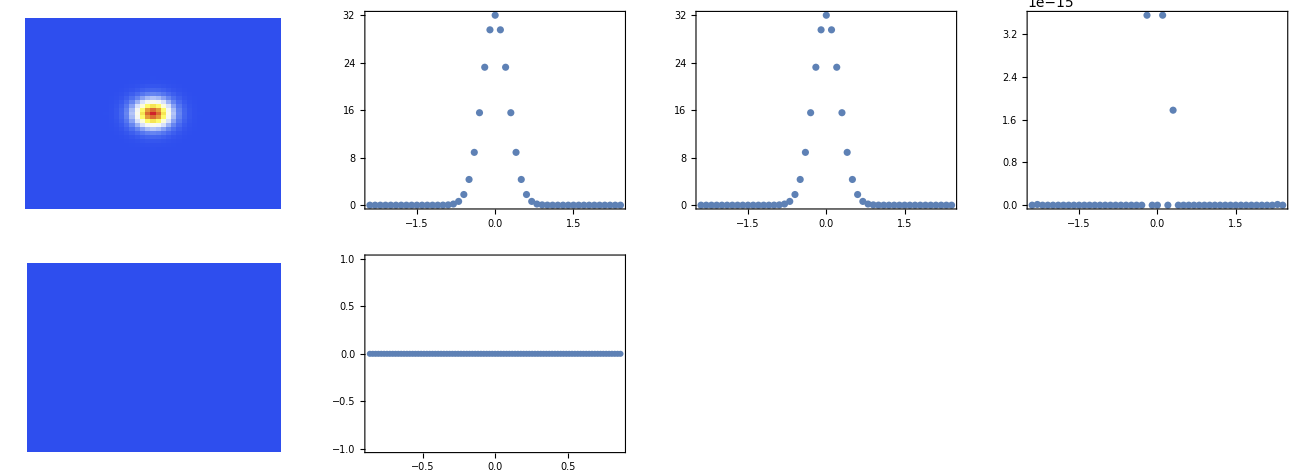

```mathematica
GraphicsGrid[
{
{
ArrayPlot[coarse2DGF⟦1⟧,ColorFunction->"TemperatureMap",PlotRange->{Full,Full,Full}],
ListPlot[coarse1DGF⟦1⟧,Axes->False,Frame->True,PlotRange->{Full,Full}],
ListPlot[analyticSolutionData,Axes->False,Frame->True,PlotRange->{Full,Full}],
ListPlot[Abs[coarse1DGF⟦1⟧-analyticSolutionData],Axes->False,Frame->True,PlotRange->{Full,Full}]
},
{
ArrayPlot[coarse2DGF⟦7⟧,ColorFunction->"TemperatureMap",PlotRange->{Full,Full,Full}],
ListPlot[coarse1DGF⟦7⟧,Axes->False,Frame->True,PlotRange->{Full,Full}]
}
},
ImageSize->13*10^2
]
```